Autor: Krzysztof Dragon

# Metody numeryczne w technice

## (kierunek informatyka)

## Projekt 2

Metoda Adamsa-Bashfortha

Napisać procedurę realizującą algorytm trzy krokowej metody Adamsa-Bashfortha (argumenty:  f, x_0, y_0, b, n).
Zminimalizować liczbę obliczeń funkcji   f. Jako metodę startową wykorzystać metodę Rungego-Kutty rzędu trzeciego.

Korzystając z napisanej procedury wyznaczyć rozwiązanie przybliżone zagadnienia początkowego:

{y'(x)=((y(x))/x^2)^(1/3),  x∈[1,50],
y(1)=1.

Obliczenia wykonać dla 10, 20 i 50 kroków.

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązania przybliżone.
Wykreślić także, na jednym rysunku, błędy uzyskanych rozwiązań przybliżonych.

## Rozwiązanie

```mathematica
(* Metoda Rungiego - Kutty rzędu trzeciego. *)
Clear[metodaRK3];
metodaRK3[f_,x0_,y0_,h_,n_] :=Module[{xw,yw,k1,k2,k3,wynik},
xw = Table[x0+i*h,{i,0,n}];
yw = Table[0,{i,0,n}];
yw[[1]] = y0;
Do[
k1=f[xw[[i]],yw[[i]]];
k2 = f[xw[[i]]+h/2,yw[[i]]+h*k1/2];
k3 = f[xw[[i+1]],yw[[i]]-h*k1+2*h*k2];
yw[[i+1]] = yw[[i]] + h/6*(k1+4k2+k3),
{i,1,n}];
wynik = Transpose[{xw,yw}];
Return[wynik]
]

Clear[MetodaAB3];
metodaAB3[f_,x0_,y0_,b_,n_] := Module[{h,xw,yw,b31,b32,b33,i,m1,m2,m3,wp,wynik},
h = (b -x0)/n;
xw = Table[x0+i*h,{i,0,n}];
yw = Table[0,{i,0,n}];
yw[[1]] = y0;

b31= 23/12;
b32 = -16/12;
b33 = 5/12;

wp = metodaRK3[f,x0,y0,h,2];

Do[yw[[i]] = wp[[i,2]], {i,2,3}];

m1 = f[xw[[2]], yw[[2]]];
m2 = f[xw[[1]], yw[[1]]];

Do[
m3 = m2;
m2 = m1;
m1 = f[xw[[i]], yw[[i]]];
yw[[i+1]] =yw[[i]] + h*(b31*m1+b32*m2+b33*m3),{i,3,n}];

wynik = Transpose[{xw,yw}];
Return[wynik];
]
```

```mathematica
(* Dane do projektu *)
f[x_,y_]:= (y/x^2)^(1/3);
x0 = 1.;
y0 = 1.;
b = 50;

(* n = 10 *)
wynik10 = metodaAB3[f,x0,y0,b,10]
```

{{1.,1.},{5.9,4.32184},{10.8,6.43924},{15.7,8.79767},{20.6,10.4207},{25.5,11.7768},{30.4,13.0164},{35.3,14.1622},{40.2,15.2321},{45.1,16.2401},{50.,17.1962}}

```mathematica
(* n = 20 *)
wynik20 = metodaAB3[f,x0,y0,b,20]
```

{{1.,1.},{3.45,2.89564},{5.9,4.25048},{8.35,5.5617},{10.8,6.59977},{13.25,7.50278},{15.7,8.32988},{18.15,9.09788},{20.6,9.81806},{23.05,10.4988},{25.5,11.146},{27.95,11.7645},{30.4,12.3579},{32.85,12.929},{35.3,13.4802},{37.75,14.0136},{40.2,14.5307},{42.65,15.0331},{45.1,15.5219},{47.55,15.9983},{50.,16.463}}

```mathematica
(* n = 50 *)
wynik50 = metodaAB3[f,x0,y0,b,50]
```

{{1.,1.},{1.98,1.85984},{2.96,2.56272},{3.94,3.1988},{4.92,3.75934},{5.9,4.26825},{6.88,4.74023},{7.86,5.18282},{8.84,5.60116},{9.82,5.99901},{10.8,6.37925},{11.78,6.74411},{12.76,7.09538},{13.74,7.43452},{14.72,7.76276},{15.7,8.08111},{16.68,8.39045},{17.66,8.69152},{18.64,8.98496},{19.62,9.27136},{20.6,9.5512},{21.58,9.82493},{22.56,10.0929},{23.54,10.3556},{24.52,10.6132},{25.5,10.866},{26.48,11.1144},{27.46,11.3585},{28.44,11.5985},{29.42,11.8347},{30.4,12.0673},{31.38,12.2963},{32.36,12.5221},{33.34,12.7446},{34.32,12.9641},{35.3,13.1806},{36.28,13.3944},{37.26,13.6054},{38.24,13.8139},{39.22,14.0198},{40.2,14.2233},{41.18,14.4245},{42.16,14.6234},{43.14,14.8202},{44.12,15.0149},{45.1,15.2075},{46.08,15.3981},{47.06,15.5869},{48.04,15.7738},{49.02,15.9589},{50.,16.1422}}

```mathematica
plt10 = ListPlot[wynik10, PlotStyle->{Red, PointSize[0.008]}];
plt20 = ListPlot[wynik20, PlotStyle->{Green, PointSize[0.008]}];
plt50 = ListPlot[wynik50, PlotStyle->{Blue, PointSize[0.008]}];
```

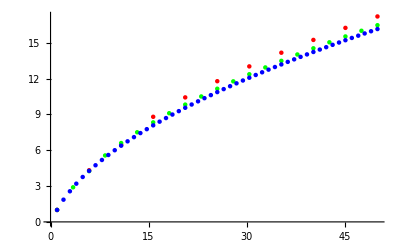

```mathematica
Show[plt10,plt20,plt50]
```

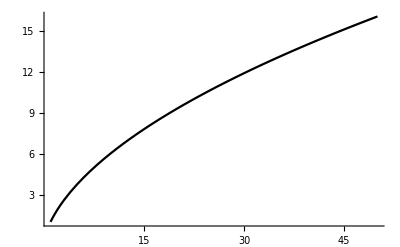

```mathematica
(* Rozwiązanie dokładne *)
roz = DSolve[{y'[x] == (y[x]/x^2)^(1/3),y[1] ==1}, y[x],x];
pdok = Plot[roz⟦1,1,2⟧,{x,1,50}, PlotRange -> All, PlotStyle->{Black, PointSize[0.008]}]
```

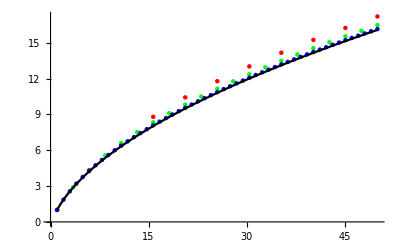

```mathematica
Show[plt10,plt20,plt50,pdok]
```

```mathematica
(* Wartości dokładne dla błędów n = 10*)
ydok = Table[roz[[1,1,2]] /. {x->wynik10[[i,1]]},{i,1,Length[wynik10]}];
bledy10 = Table [{wynik10[[i,1]], Abs[wynik10[[i,2]] - ydok[[i]]]},{i,1,Length[wynik10]}]
```

{{1.,0.},{5.9,0.0957117},{10.8,0.112223},{15.7,0.773699},{20.6,0.930096},{25.5,0.974108},{30.4,1.01475},{35.3,1.04916},{40.2,1.07819},{45.1,1.1036},{50.,1.12636}}

```mathematica
(* Wartości dokładne dla błędów n = 20 *)
ydok = Table[roz[[1,1,2]] /. {x->wynik20[[i,1]]},{i,1,Length[wynik20]}];
bledy20 = Table [{wynik20[[i,1]], Abs[wynik20[[i,2]] - ydok[[i]]]},{i,1,Length[wynik20]}]
```

{{1.,0.},{3.45,0.0202863},{5.9,0.0243546},{8.35,0.215442},{10.8,0.27276},{13.25,0.29135},{15.7,0.305904},{18.15,0.317713},{20.6,0.327468},{23.05,0.335877},{25.5,0.34333},{27.95,0.350056},{30.4,0.356207},{32.85,0.361889},{35.3,0.367179},{37.75,0.372134},{40.2,0.376801},{42.65,0.381214},{45.1,0.385404},{47.55,0.389394},{50.,0.393205}}

```mathematica
(* Wartości dokładne dla błędów n = 50 *)
ydok = Table[roz[[1,1,2]] /. {x->wynik50[[i,1]]},{i,1,Length[wynik50]}];
bledy50 = Table [{wynik50[[i,1]], Abs[wynik50[[i,2]] - ydok[[i]]]},{i,1,Length[wynik50]}]
```

{{1.,0.},{1.98,0.00171448},{2.96,0.00220234},{3.94,0.0268009},{4.92,0.0375236},{5.9,0.0421161},{6.88,0.0452039},{7.86,0.0475307},{8.84,0.0493757},{9.82,0.0509121},{10.8,0.0522374},{11.78,0.0534092},{12.76,0.0544641},{13.74,0.0554267},{14.72,0.0563145},{15.7,0.05714},{16.68,0.0579128},{17.66,0.0586403},{18.64,0.0593283},{19.62,0.0599815},{20.6,0.0606037},{21.58,0.0611981},{22.56,0.0617676},{23.54,0.0623142},{24.52,0.0628401},{25.5,0.063347},{26.48,0.0638363},{27.46,0.0643093},{28.44,0.0647673},{29.42,0.0652112},{30.4,0.0656421},{31.38,0.0660606},{32.36,0.0664677},{33.34,0.0668639},{34.32,0.0672499},{35.3,0.0676262},{36.28,0.0679935},{37.26,0.0683521},{38.24,0.0687024},{39.22,0.069045},{40.2,0.0693801},{41.18,0.0697082},{42.16,0.0700295},{43.14,0.0703443},{44.12,0.0706529},{45.1,0.0709557},{46.08,0.0712527},{47.06,0.0715443},{48.04,0.0718306},{49.02,0.072112},{50.,0.0723885}}

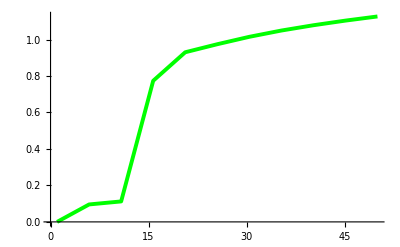

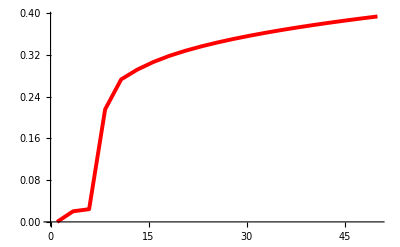

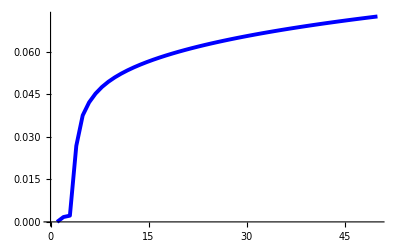

```mathematica
wb10 = ListPlot[bledy10, Joined->True, PlotStyle->{Green, Thickness -> 0.007}]
wb20 = ListPlot[bledy20, Joined->True, PlotStyle->{Red, Thickness -> 0.007}]
wb50 = ListPlot[bledy50, Joined->True, PlotStyle->{Blue, Thickness -> 0.007}]
```

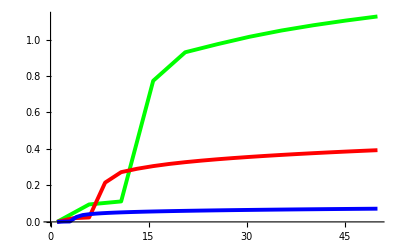

```mathematica
Show[wb10,wb20,wb50]
```